## data

```mathematica
minyear=1960.0;
maxyear=2017.0;
```

```mathematica
gdp={1900+FromDate[Normal[#[[1]]]]/(365.24*3600*24)+0.25,#[[2]]}&/@Drop[Import["C:\\Users\\dp864c\\Desktop\\SAVED DESKTOP\\GDP.xls"][[1]],11];
GDP=Interpolation[gdp,InterpolationOrder->1];
```

```mathematica
m0={1900+FromDate[Normal[#[[1]]]]/(365.24*3600*24)+1/12.,#[[2]]/1000}&/@Drop[Import["C:\\Users\\dp864c\\Desktop\\SAVED DESKTOP\\MBCURRCIR.xls"][[1]],11];
M0=Interpolation[m0,InterpolationOrder->1];
```

```mathematica
r10={1900+FromDate[Normal[#[[1]]]]/(365.24*3600*24)+1/12.,#[[2]]}&/@Drop[Import["C:\\Users\\dp864c\\Desktop\\SAVED DESKTOP\\GS10.xls"][[1]],11];
R10=Interpolation[r10,InterpolationOrder->1];
```

## fit

```mathematica
solution=FindMinimum[Total[Table[Abs[(xx Log[GDP[yy]/M0[yy]]+zz)-Log[R10[yy]]],{yy,minyear,maxyear,1/12.}]],{{xx,3.0},{zz,-10.0}},Method->"PrincipalAxis"]
X0=xx/.solution[[2]];
Z0=zz/.solution[[2]];
```

{89.6532,{xx→2.78145,zz→-6.44412}}

### graph

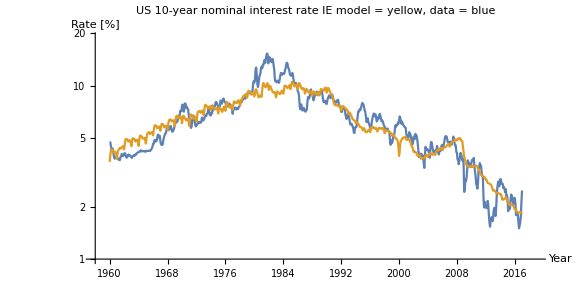

```mathematica
Show[LogPlot[{R10[yy],Exp[(X0 Log[GDP[yy]/M0[yy]]+Z0)]},{yy,minyear,maxyear},BaseStyle->{FontSize->13},Axes->True,ImageSize->Large,Frame->False,AspectRatio->1/2,PlotRange->{{minyear-2,maxyear+2},{1,19}},AxesLabel->{"Year "," Rate [%]"},PlotLabel->"\nUS 10-year nominal interest rate\nIE model = yellow, data = blue"]]
```